```mathematica
计算3个电荷产生的电力线——折线法
```

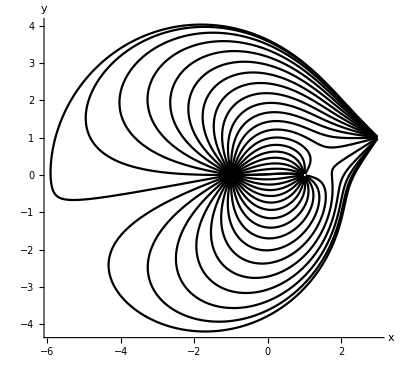

```mathematica
p1={1,0};p2={-1,0};p3={3,1};
q1=1.0;q2=-2.0;q3=5.0;forceline={};
ψ=q1/(√((x-1)^2+y^2))+q2/(√((x+1)^2+y^2))+
q3/(√((x-3)^2+(y-1)^2));
field=-D[ψ,x]-ⅈ*D[ψ,y];
step=0.03;r1=0.02;r2=15;
Do[
θ=ϕ;single={p2};
Label[ss];p=Last[single];
p=p-step*{Cos[θ],Sin[θ]};
θ=Arg[field/.{x->p[[1]],y->p[[2]]}];
If[(Norm[p1-p]>r1)∧(Norm[p2-p]>r1)∧
(Norm[p3-p]>r1)∧(Norm[p]<r2),
AppendTo[single,p];Goto[ss]];
AppendTo[forceline,single],
{ϕ,-π,π,π/18}]
Show[
Graphics[{Thickness[0.004],Line/@forceline}],
PlotRange->All,AspectRatio->Automatic,
AxesStyle->Thickness[0.003],
AxesLabel->{"x","y"},Axes->True]
Clear[x,y]
```